Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

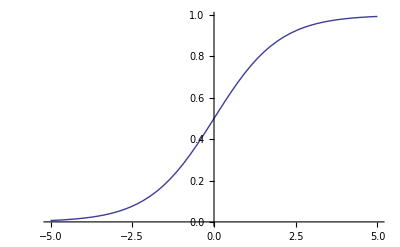

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Declarations

```mathematica
SeedRandom[1]
W=Weight[4,5]
V=Visibles[4]
H=Hiddens[5]
BH=BiasHiddenSampling[5]
BV=BiasVisibleSampling[4]
```

{{0.634779,-0.777161,0.579052,-0.624394,-0.517278},{-0.868522,0.0844932,-0.537691,-0.207988,0.400948},{-0.576348,0.497314,-0.154299,-0.50501,0.954344},{0.650326,0.85055,0.156112,-0.414261,-0.583898}}

{1,0,0,1}

{0,1,0,0,1}

{0,0,0,0,0}

{0,0,0,0}

```mathematica
dataV=Table[Visibles[4],{i,10}]
```

{{0,0,1,1},{0,0,1,1},{1,1,1,1},{0,0,1,1},{1,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,0,0},{0,1,0,1},{0,1,1,0}}

```mathematica
V2=Visibles[4]
```

{1,1,1,0}

```mathematica
V3=Visibles[4]
```

{0,1,0,0}

### Sampling Functions

```mathematica
sample[l_]:=Map[RandomVariate[BernoulliDistribution[#]]&,l]
SampleHidden[w_,bh_][v_]:=sample[Logistic@(wᵀ.v+bh)]
SampleVisible[w_,bv_][h_]:=sample[Logistic@(w.h+bv)]
HiddenProbabilities[w_,bh_][v_]:=Logistic@(wᵀ.v+bh);
VisibleProbabilities[w_,bv_][h_]:=Logistic@(w.h+bv);
```

## Learning

```mathematica
ClearAll[DataLearning,DeltaWeight]
```

```mathematica
DeltaWeight[bh_,bv_,ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew},
wnew=w;
Do[
h1=SampleHidden[w,bh][v1];
v2=SampleVisible[w,bv][h1];
h2=SampleHidden[w,bh][v2];

w0=1-Outer[BitXor,v1,h1];
w1=1-Outer[BitXor,v1,h2];
(*
w0=Outer[Times,v1,HiddenProbabilities[wnew,bh][v1]];
w1=Outer[Times,v1,HiddenProbabilities[wnew,bh][v2]];*)
wnew+= ϵ*(w0-w1);
,
{4}];
wnew
]
```

```mathematica
DataLearning[w_,bh_,bv_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[bh,bv,ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,bh_,bv_,ϵ_,n_,dataV_]:=Module[{w1,w2,w3},w1=Nest[Function[DeltaWeight[bh,bv,ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[Function[DeltaWeight[bh,bv,ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[Function[DeltaWeight[bh,bv,ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
]
```

## Testing

```mathematica
SeedRandom[4];
BH1=RandomReal[{-0.1,0.1},4];
BV1=RandomReal[{-0.1,0.1},4];
W=RandomReal[{-0.1,0.1},{4,4}];
dataV={{0,0,1,1},{1,1,1,1},{0,1,0,1},{1,0,1,0}};
w1=StepLearning[W,BH1,BV1,0.01,3000,dataV];
#->HiddenProbabilities[w1,BH1][#]&/@dataV
#-> ArrayPlot[List @ VisibleProbabilities[w1,BV1][#],PixelConstrained->10,Mesh->True,ColorFunctionScaling->False]& /@Tuples[{0,1},4]
```

{{0,0,1,1}→{0.475033,0.9301,0.992802,0.0287166},{1,1,1,1}→{0.993364,0.00855583,0.989161,0.0269317},{0,1,0,1}→{0.0577356,0.00147567,0.999462,0.828441},{1,0,1,0}→{0.999575,0.855427,0.0479832,0.00529382}}

{{0,0,0,0}→-Graphics-,{0,0,0,1}→-Graphics-,{0,0,1,0}→-Graphics-,{0,0,1,1}→-Graphics-,{0,1,0,0}→-Graphics-,{0,1,0,1}→-Graphics-,{0,1,1,0}→-Graphics-,{0,1,1,1}→-Graphics-,{1,0,0,0}→-Graphics-,{1,0,0,1}→-Graphics-,{1,0,1,0}→-Graphics-,{1,0,1,1}→-Graphics-,{1,1,0,0}→-Graphics-,{1,1,0,1}→-Graphics-,{1,1,1,0}→-Graphics-,{1,1,1,1}→-Graphics-}